```mathematica
rules={"P" -> "", "P" -> "0","P" -> "1","P" -> "0P0","P" -> "1P1"}
```

{P→,P→0,P→1,P→0P0,P→1P1}

```mathematica
StringReplaceList["P", rules]
```

{,0,1,0P0,1P1}

```mathematica
NestList[StringReplaceList[#, rules]&, "P",2]
```

{P,{,0,1,0P0,1P1},{{},{},{},{00,000,010,00P00,01P10},{11,101,111,10P01,11P11}}}

```mathematica
productionRule[s0_, rules_, n_] := Union[Flatten[NestList[Flatten[StringReplaceList[#, rules]]&, s0,n] ]]
```

```mathematica
productionRule["P", rules, 5]
```

{,0,00,000,0000,00000,000000,0000000,00000000,000000000,00000P00000,000010000,00001P10000,0000P0000,0001000,000101000,00010P01000,00011000,000111000,00011P11000,0001P1000,000P000,00100,001000100,00100100,00100P00100,0010100,001010100,00101P10100,0010P0100,001100,001101100,00110P01100,0011100,00111100,001111100,00111P11100,0011P1100,001P100,00P00,010,010000010,01000010,0100010,01000P00010,010010,010010010,01001P10010,0100P0010,01010,0101010,010101010,01010P01010,01011010,010111010,01011P11010,0101P1010,010P010,0110,011000110,01100110,01100P00110,011010110,0110110,01101P10110,0110P0110,01110,011101110,01110P01110,011110,0111110,01111110,011111110,01111P11110,0111P1110,011P110,01P10,0P0,1,100000001,10000001,1000001,100001,10000P00001,10001,100010001,10001P10001,1000P0001,1001,1001001,100101001,10010P01001,10011001,100111001,10011P11001,1001P1001,100P001,101,101000101,10100101,10100P00101,10101,1010101,101010101,10101P10101,1010P0101,101101,101101101,10110P01101,1011101,10111101,101111101,10111P11101,1011P1101,101P101,10P01,11,110000011,11000011,1100011,11000P00011,110010011,110011,11001P10011,1100P0011,110101011,1101011,11010P01011,11011,11011011,110111011,11011P11011,1101P1011,110P011,111,111000111,11100111,11100P00111,111010111,1110111,11101P10111,1110P0111,1111,111101111,11110P01111,11111,111111,1111111,11111111,111111111,11111P11111,1111P1111,111P111,11P11,1P1,P}

```mathematica
isValidQ[ string_,s0_, rules_] := MemberQ[productionRule[s0, rules,StringLength[string]], string]
```

```mathematica
isValidQ["00100", "P", rules]
```

True

```mathematica
rp = productionRule["P", rules, 3]
```

{,0,00,000,0000,00000,000P000,00100,001P100,00P00,010,01010,010P010,0110,01110,011P110,01P10,0P0,1,10001,1001,100P001,101,10101,101P101,10P01,11,11011,110P011,111,1111,11111,111P111,11P11,1P1,P}

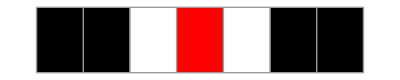

```mathematica
ArrayPlot[{Characters[rp[[9]]]}, ColorRules-> {"0" -> Black, "1" -> White, "P" -> Red}, Mesh->True]
```

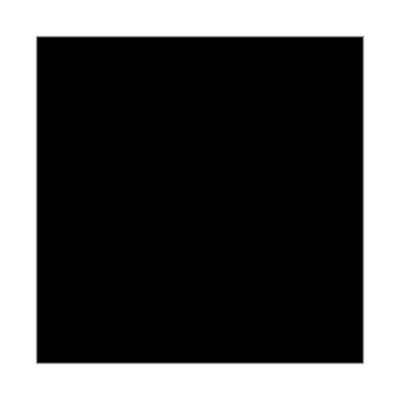
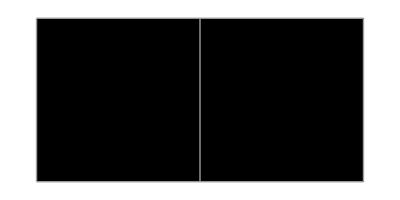
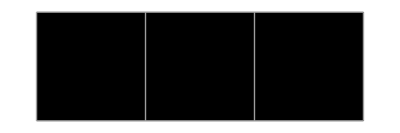
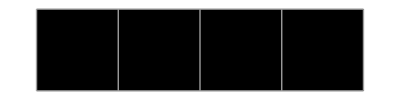
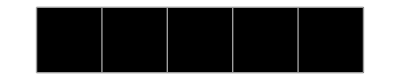
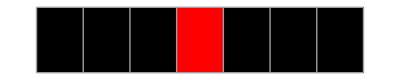
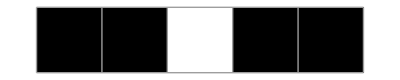
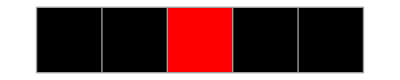

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ArrayPlot[{Characters[#]}, ColorRules-> {"0" -> Black, "1" -> White, "P" -> Red}, Mesh->True]&, rp]
```